```mathematica
SetDirectory[NotebookDirectory[]]
countsRaw=Import["protein_based_rec_scores_counts_string_mst.tsv"];
Length[countsRaw]
counts=countsRaw;
counts[[All,8;;14]]=ToExpression/@ countsRaw[[All,8;;14]];
talliedCounts=GatherBy[counts,{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[Sort[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedCounts]]
```

/Users/hayssam/Documents/ISOP_0.2/tests

496

ar | 9630 | LSI | 25%Prot,0%Docs,MST/STRING | 25
ar | 9630 | LSI | 25%Prot,1%Docs,MST/STRING | 25
ar | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 30
ar | 9630 | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25
ar | 9630 | LSI+STRING | 25%Prot,1%Docs,MST/STRING | 25
ar | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 30
egfr | 9630 | LSI | 25%Prot,0%Docs,MST/STRING | 25
egfr | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 5
egfr | 9630 | LSI | 25%Prot,50%Docs,MST/STRING | 25
egfr | 9630 | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25
egfr | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5
egfr | 9630 | LSI+STRING | 25%Prot,50%Docs,MST/STRING | 25
hsa04010 | 9630 | LSI | TF+MEMB,MST/STRING,0 docs | 6
hsa04010 | 9630 | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 6
hsa04012 | 9630 | LSI | TF+MEMB,MST/STRING,0 docs | 11
hsa04012 | 9630 | LSI | TF+MEMB,MST/STRING,KEGG REFS | 11
hsa04012 | 9630 | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 11
hsa04012 | 9630 | LSI+STRING | TF+MEMB,MST/STRING,KEGG REFS | 11
il2 | 9630 | LSI | 25%Prot,0%Docs,MST/STRING | 25
il2 | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 25
il2 | 9630 | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25
il2 | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 25
tcell | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 5
tcell | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5
tgfb | 9630 | LSI | 25%Prot,0%Docs,MST/STRING | 25
tgfb | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 5
tgfb | 9630 | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25
tgfb | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5

## Comparing average

We group by PW, possible edges and scoring fun

```mathematica
countStyle={Black,Dashed,Dashed};
RocStyle={Black,Red,{Gray,Dashed}};
```

```mathematica
talliedCounts=GatherBy[counts,{#[[1]],#[[6]],#[[14]],#[[15]]}&];
```

```mathematica
Length[talliedCounts[[1]]]
```

6

```mathematica
Length /@ talliedCounts
```

{6,6,1,1,1,1}

Plot them all

```mathematica
PlotForRow[row_]:=Module[{label,realPosEdges,realPosProt,possibleProt,possibleEdges,xlimE,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveEdges,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,proteinPoints,edgesPointsString,proteinPointsString,tpr,fpr,roc,tprString,fprString,rocString},
label=row[[1]];
realPosEdges=row[[5]];
realPosProt=row[[4]];
possibleProt=row[[6]];
possibleEdges=row[[7]];
xlimE=row[[5]]*3;
xlimProt=row[[4]]*3;
ylimE=row[[5]]*1.5;
ylimProt=row[[4]]*1.5;
neighborStr=If[possibleProt>9000,"Whole","In neighbor"];
optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[row[[11]],row[[12]]],2];
proteinPoints=Partition[Riffle[row[[8]],row[[9]]],2];
tpr=row[[12]]/realPosEdges;
fpr=row[[13]]/possibleEdges;
roc=Partition[Riffle[fpr,tpr],2];

{label,
neighborStr,
ListLinePlot[{edgesPoints,optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->countStyle],
ListLinePlot[{proteinPoints,optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->countStyle],
ListLinePlot[{roc,{{0,0},{1,1}}},PlotRange->{{0,0.1},{0,1}},PlotStyle->RocStyle],ListLinePlot[{roc,{{0,0},{1,1}}},PlotRange->{{0,1},{0,1}},PlotStyle->RocStyle]
}
]
```

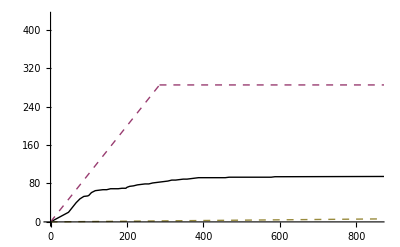
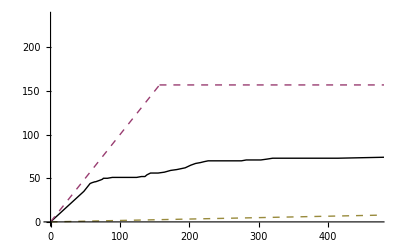
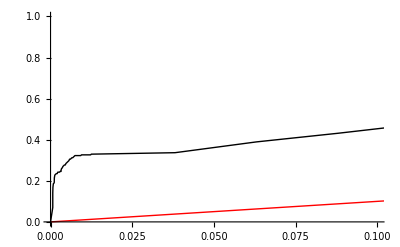
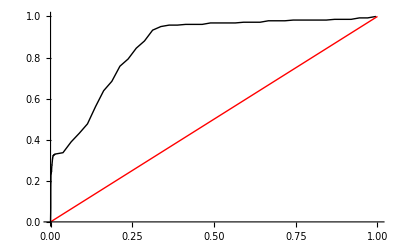
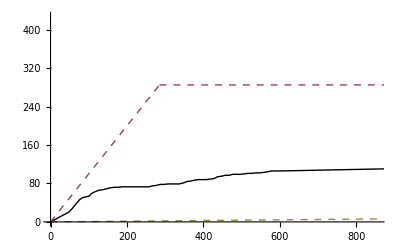
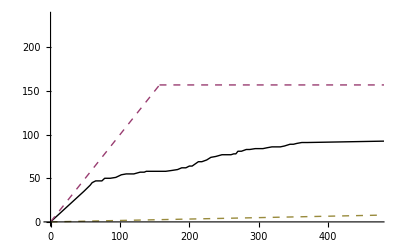
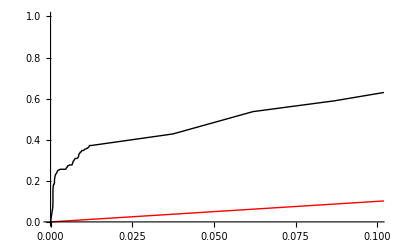
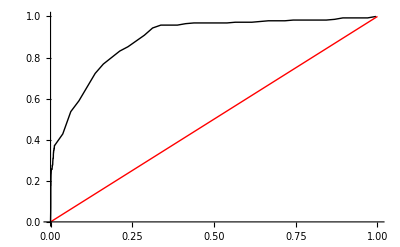
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-
hsa04010 | Whole | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
PlotForRow[#]&/@talliedCounts[[1]]
]
```

```mathematica
rows=talliedCounts[[1]];
```

```mathematica
PlotForRows[rows_,style_:{Hue[0.65,0.5,0.8,1],Thick}]:=Module[{label,method,realPosEdges,realPosProt,possibleProt,possibleEdges,nReps,xlimE,optTag,xlimProt,ylimE,ylimProt,neighborStr,optimalCurveProt,chancePickingPositiveEdge,chancePickingPositiveProt,edgesPoints,protsPoints,rocs,optimalCurveEdges},
label=ToUpperCase[rows[[1,1]]];
method=rows[[1,14]];
realPosEdges=rows[[1,5]];
realPosProt=rows[[1,4]];
possibleProt=rows[[1,6]];
possibleEdges=rows[[1,7]];
nReps=Length[rows];
xlimE=rows[[1,5]]*4;
optTag=rows[[1,15]];
xlimProt=rows[[1,4]]*4;
ylimE=rows[[1,5]]*1.25;
ylimProt=rows[[1,4]]*1.25;
neighborStr=If[possibleProt>9000,"HPRD",Grid[{{"Neighborhood"},{StringForm["`` prots",possibleProt]},{StringForm["`` edges",possibleEdges]}}]];optimalCurveEdges={{0,0},{realPosEdges,realPosEdges},{10000,realPosEdges}};
optimalCurveProt={{0,0},{realPosProt,realPosProt},{10000,realPosProt}};
chancePickingPositiveEdge={{0,0},{xlimE,xlimE*realPosEdges/possibleEdges}};
chancePickingPositiveProt={{0,0},{xlimProt,xlimProt*realPosProt/possibleProt}};
edgesPoints=Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,11,2;;]],rows[[All,12,2;;]]}];
protsPoints=Partition[Riffle[#[[1]],#[[2]]],2]& /@ Transpose[{rows[[All,8,2;;]],rows[[All,9,2;;]]}];
rocs=Partition[Riffle[#[[13,2;;]]/possibleEdges,#[[12,2;;]]/realPosEdges],2]&/@ rows;
{
label,
neighborStr,
method,
optTag,
nReps,
Show[
ListLinePlot[{optimalCurveEdges,chancePickingPositiveEdge},PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->{Dashed,Dashed}],
ListLinePlot[edgesPoints,PlotRange->{{0,xlimE},{0,ylimE}},PlotStyle->style]
],
Show[
ListLinePlot[{optimalCurveProt,chancePickingPositiveProt},PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->{Dashed,Dashed}],
ListLinePlot[protsPoints,PlotRange->{{0,xlimProt},{0,ylimProt}},PlotStyle->style]
],
Show[
ListLinePlot[{{0,0},{1,1}},PlotRange->{{0,0.1},{0,1}},PlotStyle->Dashed],
ListLinePlot[rocs,PlotRange->{{0,0.1},{0,1}},PlotStyle->style]
],
Show[
ListLinePlot[{{0,0},{1,1}},PlotRange->{{0,1},{0,1}},PlotStyle->Dashed],
ListLinePlot[rocs,PlotRange->{{0,1},{0,1}},PlotStyle->style]
]
}
]
```

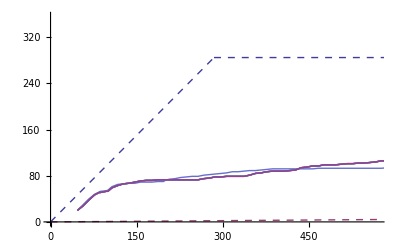
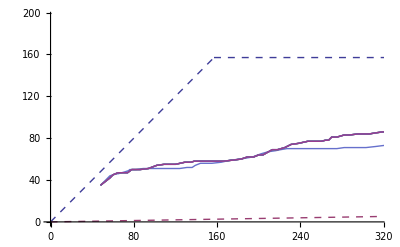
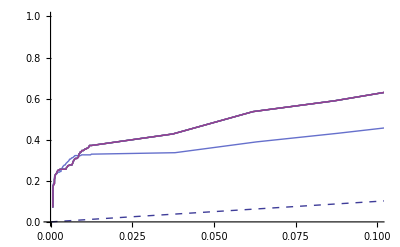
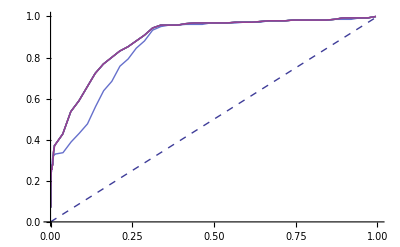
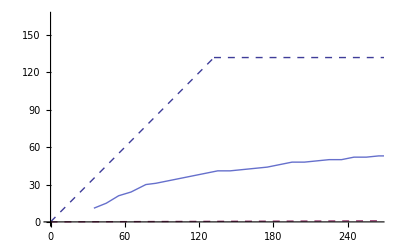
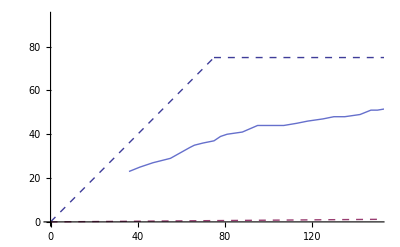
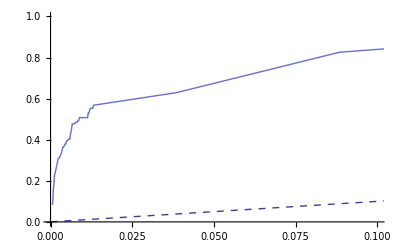
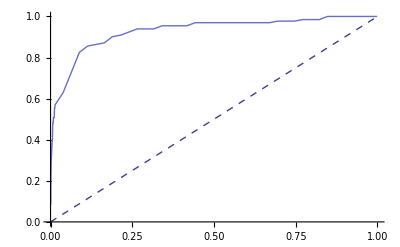
HSA04010 | HPRD | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | TF+MEMB,STRING,0 docs | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | TF+MEMB,STRING,KEGG REFS | 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
PlotForRows[#]&/@Select[talliedCounts,Position[#[[1,14]],STRING]≠{}&],Frame->All
]
```

## Comparing LSI to LSI+STRING For HSA04010

hsa04010 | 9630 | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 6
hsa04010 | 9630 | LSI | TF+MEMB,MST/STRING,0 docs | 6

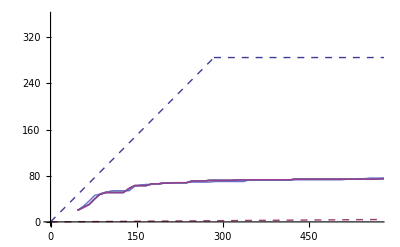
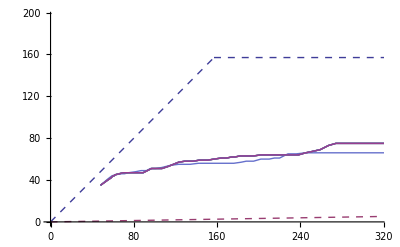
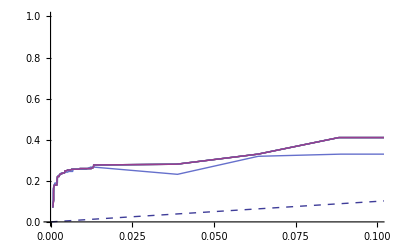
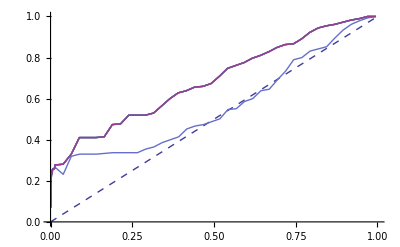
HSA04010 | HPRD | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | TF+MEMB,MST/STRING,0 docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
rows=GatherBy[Select[counts,#[[1]]=="hsa04010"&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ rows,Frame->All]
Grid[
PlotForRows[#]&/@rows
,Frame->All]
```

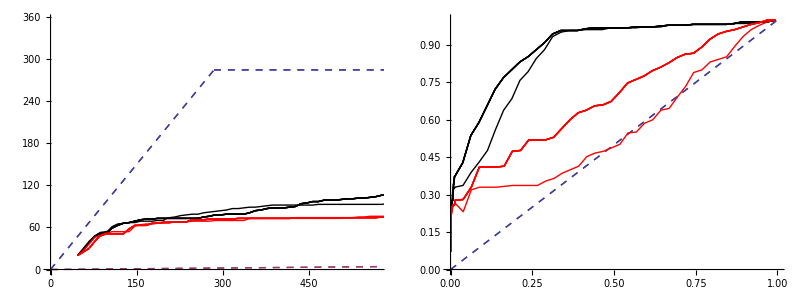

```mathematica
Grid[{{Show[
{PlotForRows[rows[[1]],{Black}][[6]],PlotForRows[rows[[2]],{Red}][[6]]}
],
Show[
{PlotForRows[rows[[1]],{Black}][[9]],PlotForRows[rows[[2]],{Red}][[9]]}
]}}]
```

## Comparing LSI to LSI+STRING For NP Pw

tgfb | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5
tgfb | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 5

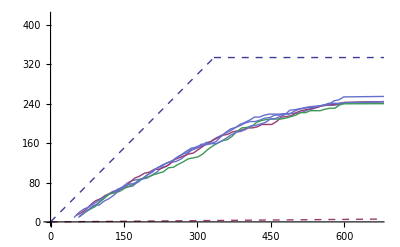
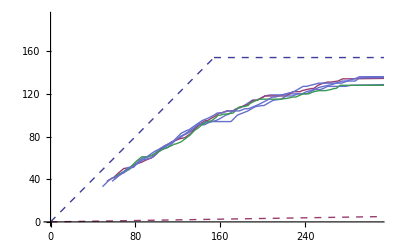
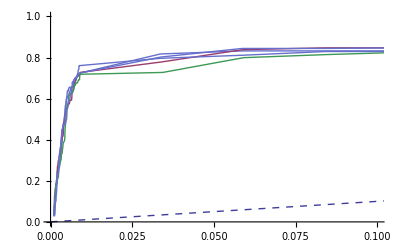
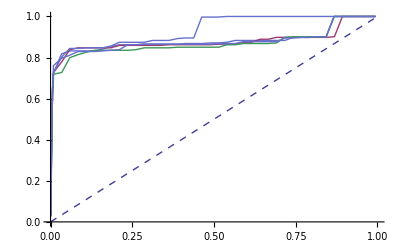
TGFB | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
rows=GatherBy[Select[counts,#[[1]]=="tgfb"&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ rows,Frame->All]
Grid[
PlotForRows[#]&/@rows
,Frame->All]
```

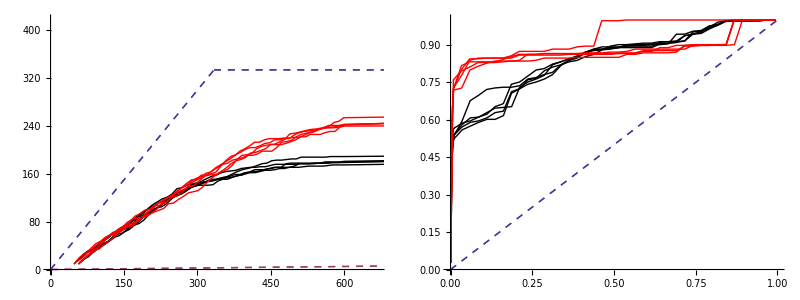

```mathematica
Grid[{{Show[
{PlotForRows[rows[[1]],{Black}][[6]],PlotForRows[rows[[2]],{Red}][[6]]}
],
Show[
{PlotForRows[rows[[1]],{Black}][[9]],PlotForRows[rows[[2]],{Red}][[9]]}
]}}]
```

ar | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5
ar | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 5

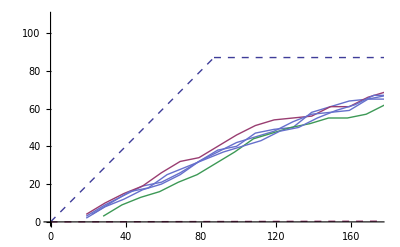
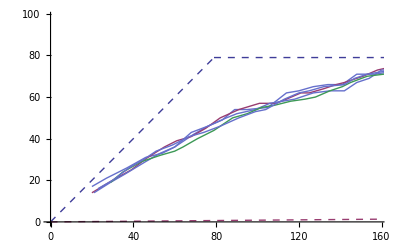
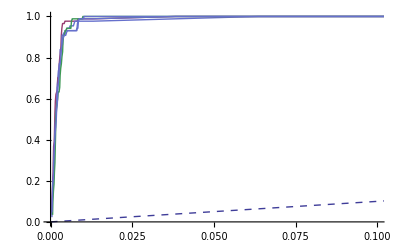
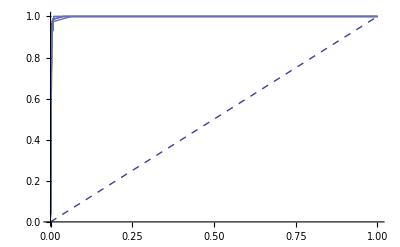
AR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
rows=GatherBy[Select[counts,#[[1]]=="ar"&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ rows,Frame->All]
Grid[
PlotForRows[#]&/@rows
,Frame->All]
```

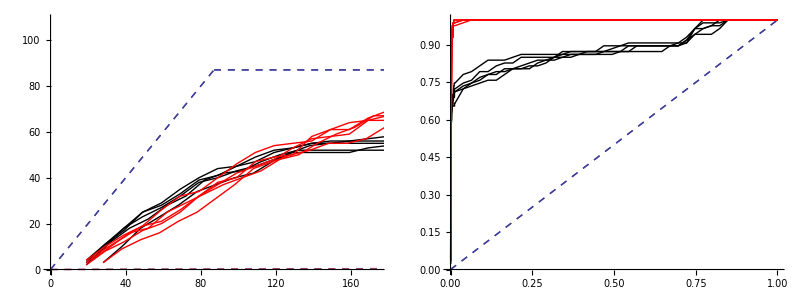

```mathematica
Grid[{{Show[
{PlotForRows[rows[[1]],{Black}][[6]],PlotForRows[rows[[2]],{Red}][[6]]}
],
Show[
{PlotForRows[rows[[1]],{Black}][[9]],PlotForRows[rows[[2]],{Red}][[9]]}
]}}]
```

## Do I find back results comparable to the one in table discussed with LW?

```mathematica
talliedRes=GatherBy[Select[counts,#[[1]]=="egfr"∧#[[6]]>3000&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedRes]
```

egfr | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
egfr | 9630 | LSI | 25%Prot,25%Docs | 30
egfr | 9630 | LSI+STRING | 25%Prot,25%Docs,STRING | 13
egfr | 9630 | LSI | 25%Prot,25%Docs,STRING | 13

```mathematica
rows=talliedRes[[-2]];
{#[[1]],#[[6]],#[[14]],#[[15]]}&[rows[[1]]]
edgesPoints=Union[Partition[Riffle[#[[1]],#[[2]]],2]]& /@ Transpose[{rows[[All,11,2;;]],rows[[All,12,2;;]]}];
protsPoints=Union[Partition[Riffle[#[[1]],#[[2]]],2]]& /@ Transpose[{rows[[All,8,2;;]],rows[[All,9,2;;]]}];
edgesFs  = Interpolation /@ edgesPoints;
protFs  = Interpolation /@ protsPoints;
```

{hsa04012,9630,LSI+STRING,TF+MEMB,0 docs,STRING}

```mathematica
N[#[77]&/@edgesFs ]
Mean[%]
N[#[51]&/@protFs ]
Mean[%]
```

{22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.,22.}

22.

{25.3513,25.276,25.3513,25.276,25.276,25.276,25.276,25.3513,25.3513,25.276,25.276,25.276,25.276,25.276,25.276,25.276,25.3513,25.276,25.276,25.276,25.276,25.3513,25.276,25.276,25.276}

25.2941

## Results with STRING MST

```mathematica
EvalAtKnowThr[rows_]:=Module[{edgesPoints,protsPoints,edgesFs,protFs},
edgesPoints=Union[Partition[Riffle[#[[1]],#[[2]]],2]]& /@ Transpose[{rows[[All,11,2;;]],rows[[All,12,2;;]]}];
protsPoints=Union[Partition[Riffle[#[[1]],#[[2]]],2]]& /@ Transpose[{rows[[All,8,2;;]],rows[[All,9,2;;]]}];
edgesFs  = Interpolation /@ edgesPoints;
protFs  = Interpolation /@ protsPoints;
Quiet[{Table[{i,Mean[N[#[i]&/@edgesFs ]]},{i,{77,85,100,200,300,500}}],
Table[{i,Mean[N[#[i]&/@protFs ]]},{i,{50,60,70,90,100,150,200,300}}]
}]
]
```

```mathematica
talliedRes=GatherBy[Select[counts,#[[1]]=="tgfb"∧#[[6]]>3000&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedRes]
```

tgfb | 9630 | LSI+STRING | 25%Prot,25%Docs | 81
tgfb | 9630 | LSI | 25%Prot,25%Docs | 81
tgfb | 9630 | LSI+STRING | 25%Prot,25%Docs,STRING | 20
tgfb | 9630 | LSI | 25%Prot,25%Docs,STRING | 20
tgfb | 9630 | LSI+STRING | 25%Prot,0%Docs | 4
tgfb | 9630 | LSI | 25%Prot,0%Docs | 4

```mathematica
rowsNoStringStringSim=talliedRes[[3]];
rowsNoStringNoStringSim=talliedRes[[4]];
rowsString=talliedRes[[1]];
rowsStringMstNoString=talliedRes[[2]];
```

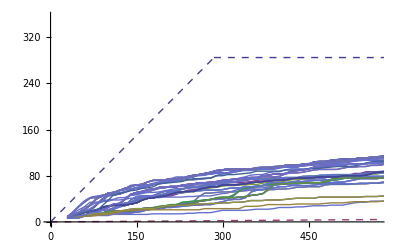
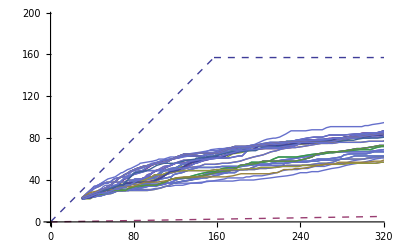
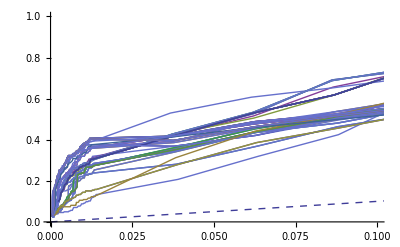
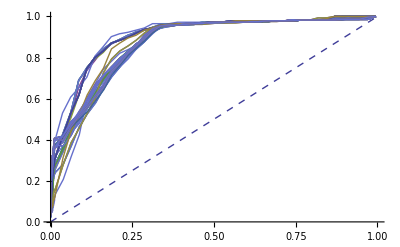
{HSA04010,HPRD,LSI+STRING,TF+MEMB,0 docs,63,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

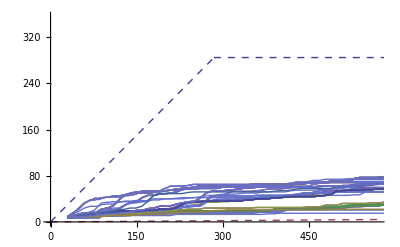
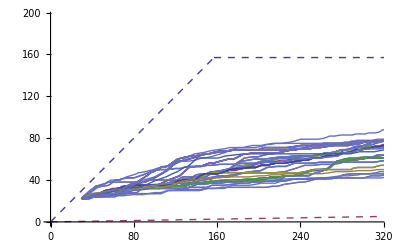
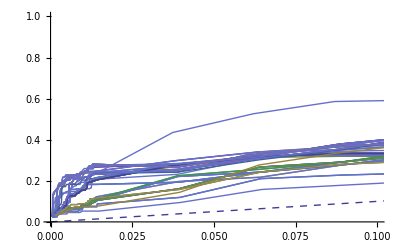
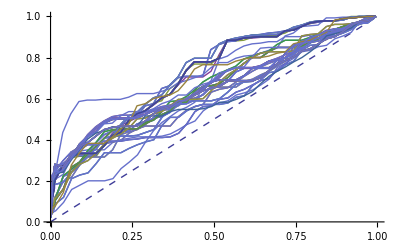
{HSA04010,HPRD,LSI,TF+MEMB,0 docs,63,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

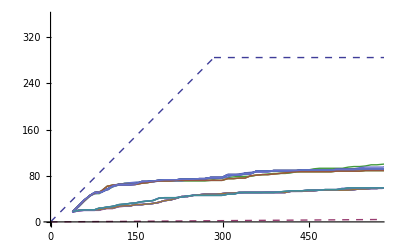
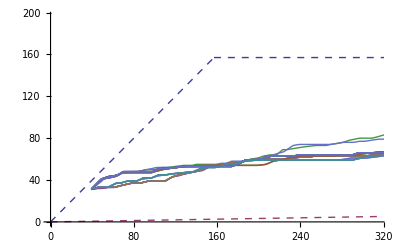
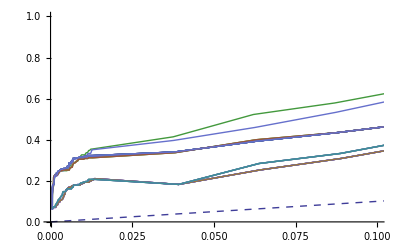
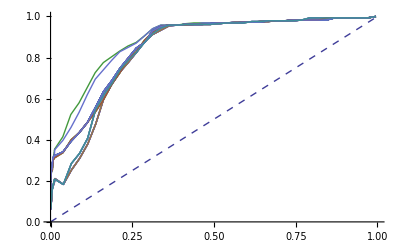
{HSA04010,HPRD,LSI+STRING,TF+MEMB,0 docs,STRING,30,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

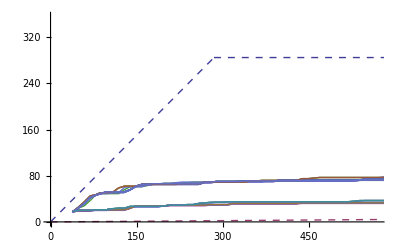
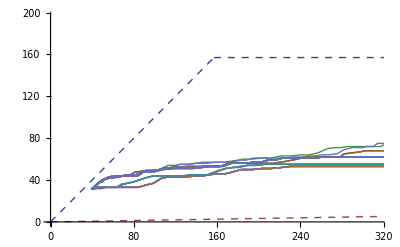
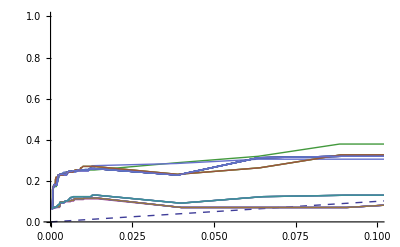
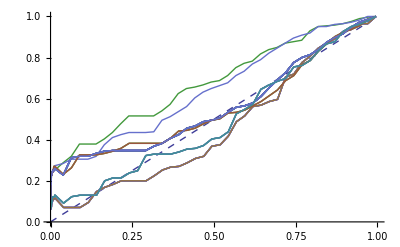
{HSA04010,HPRD,LSI,TF+MEMB,0 docs,STRING,30,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

({{77,21.4127},{85,23.8254},{100,29.},{200,49.0159},{300,63.8249},{500,83.4776}}
{{50,29.0869},{60,32.191},{70,35.4385},{90,41.1715},{100,43.4899},{150,56.8278},{200,65.6126},{300,75.9435}})

({{77,14.6508},{85,15.9683},{100,17.9365},{200,29.4762},{300,40.7045},{500,50.862}}
{{50,27.4271},{60,29.1364},{70,30.6983},{90,35.175},{100,36.7669},{150,48.1669},{200,54.4351},{300,66.5529}})

({{77,38.5333},{85,39.7333},{100,44.4},{200,58.9667},{300,64.9627},{500,76.4466}}
{{50,37.7668},{60,39.7731},{70,43.163},{90,44.5812},{100,45.5453},{150,52.9028},{200,59.0854},{300,65.3218}})

({{77,35.8},{85,37.6333},{100,39.3},{200,50.6},{300,54.379},{500,57.1}}
{{50,36.6219},{60,38.9325},{70,40.2337},{90,44.1893},{100,45.3506},{150,49.8879},{200,55.205},{300,59.9215}})

```mathematica
PlotForRows[rowsNoStringStringSim]
PlotForRows[rowsNoStringNoStringSim]
PlotForRows[rowsString]
PlotForRows[rowsStringMstNoString]
EvalAtKnowThr[rowsNoStringStringSim]//MatrixForm
EvalAtKnowThr[rowsNoStringNoStringSim]//MatrixForm
EvalAtKnowThr[rowsString]//MatrixForm
EvalAtKnowThr[rowsStringMstNoString]//MatrixForm
```

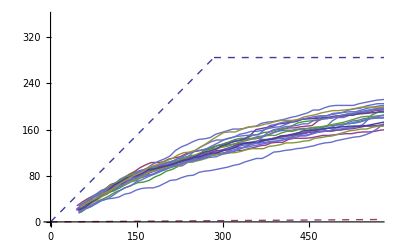
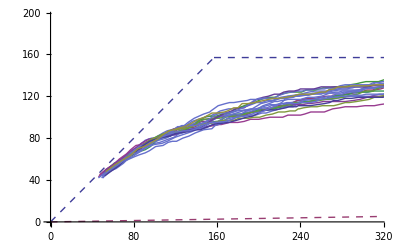
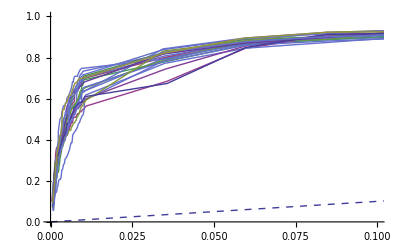
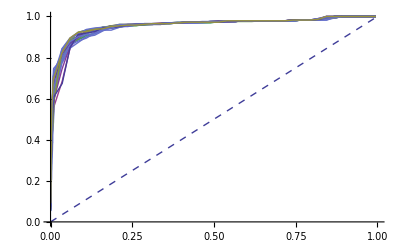
{HSA04010,HPRD,LSI+STRING,25%Prot,25%Docs,20,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{77,39.5182},{85,44.3289},{100,53.0373},{200,96.4011},{300,128.728},{500,172.201}},{{50,44.1766},{60,52.6393},{70,59.3416},{90,72.7441},{100,77.7952},{150,95.3339},{200,108.774},{300,124.593}}}

```mathematica
hsa04010KeggRefsTFMemb=talliedRes[[7]];
PlotForRows[hsa04010KeggRefsTFMemb]
EvalAtKnowThr[hsa04010KeggRefsTFMemb]
```

## Results on NP with STRING MST

```mathematica
talliedRes=GatherBy[Select[counts,#[[1]]=="egfr"∧#[[6]]>3000&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedRes]
```

egfr | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
egfr | 9630 | LSI | 25%Prot,25%Docs | 30
egfr | 9630 | LSI+STRING | 25%Prot,25%Docs,STRING | 30
egfr | 9630 | LSI | 25%Prot,25%Docs,STRING | 30

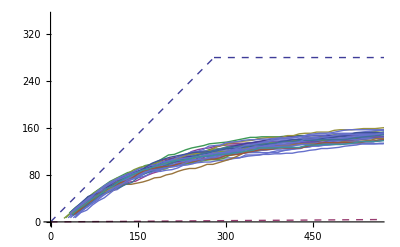
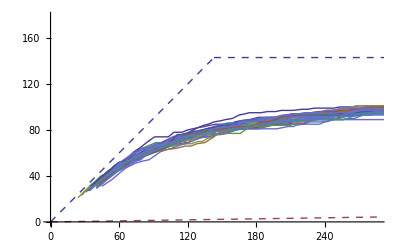
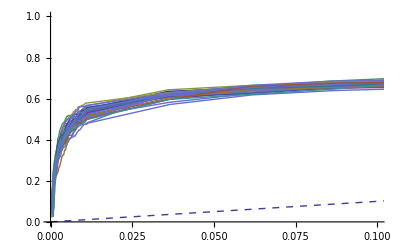
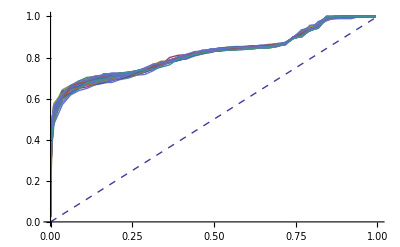
{EGFR,HPRD,LSI+STRING,25%Prot,25%Docs,STRING,30,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{77,43.1095},{85,48.4783},{100,57.2979},{200,98.6568},{300,120.137},{500,142.532}},{{50,40.5417},{60,47.6335},{70,53.7769},{90,63.4112},{100,67.0636},{150,81.0131},{200,88.5319},{300,97.2571}}}

```mathematica
PlotForRows[talliedRes[[3]]]
EvalAtKnowThr[talliedRes[[3]]]
```

```mathematica
talliedRes=GatherBy[Select[counts,#[[1]]=="ar"∧#[[6]]>3000&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedRes]
```

ar | 9630 | LSI+STRING | 25%Prot,25%Docs | 30
ar | 9630 | LSI | 25%Prot,25%Docs | 30
ar | 9630 | LSI+STRING | 25%Prot,25%Docs,STRING | 30
ar | 9630 | LSI | 25%Prot,25%Docs,STRING | 30

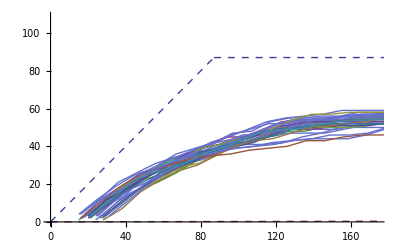
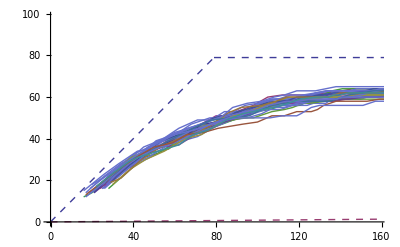
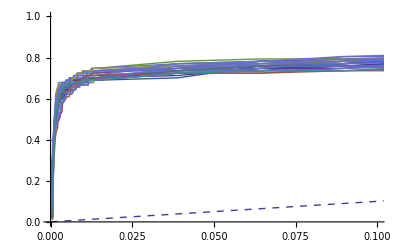
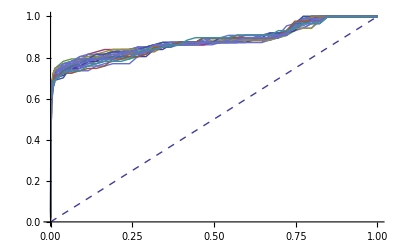
{AR,HPRD,LSI+STRING,25%Prot,25%Docs,STRING,30,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{77,34.9891},{85,37.6172},{100,42.5236},{200,55.3471},{300,58.0523},{500,61.0992}},{{50,35.2734},{60,39.7155},{70,44.1861},{90,51.3788},{100,54.314},{150,61.3691},{200,63.1484},{300,65.7989}}}

```mathematica
PlotForRows[talliedRes[[3]]]
EvalAtKnowThr[talliedRes[[3]]]
```

```mathematica
Position[talliedRes[[1,1,14]],STRING]
```

{{2}}

```mathematica
talliedRes=GatherBy[Select[counts,StringPosition[#[[15]],"STRING"]≠{} ∧#[[6]]>3000∧Position[#[[14]],STRING]≠{}&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedRes]
```

tgfb | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 20
ar | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 30
egfr | 9630 | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 30

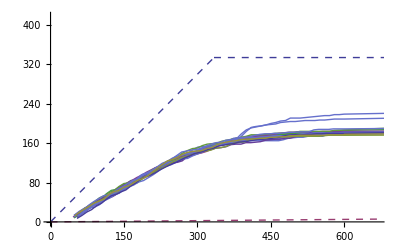
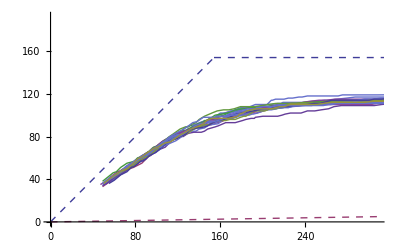
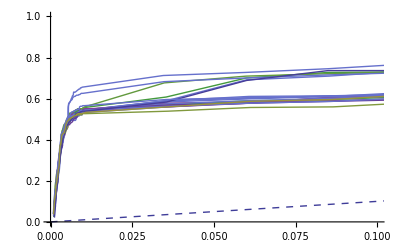
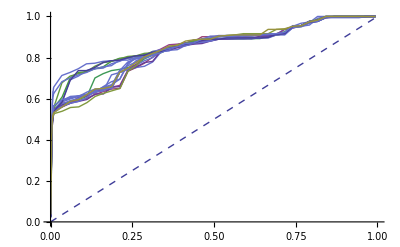
TGFB | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 20 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[PlotForRows /@ talliedRes]
```

## Vs LSI wo STRING

```mathematica
talliedRes=GatherBy[Select[counts,StringPosition[#[[15]],"STRING"]≠{} ∧#[[6]]>3000∧Position[#[[14]],STRING]=={}&],{#[[1]],#[[6]],#[[14]],#[[15]]}&];
Grid[{#[[1,1]],#[[1,6]],#[[1,14]],#[[1,15]],Length[#]}&/@ talliedRes]
```

tgfb | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 20
ar | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 30
egfr | 9630 | LSI | 25%Prot,25%Docs,MST/STRING | 30

```mathematica
Grid[PlotForRows /@ talliedRes]
```

TGFB | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 20 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Figures for manuscript

```mathematica
rows=Select[talliedCounts,Position[#[[1,14]],STRING]≠{}∧StringPosition[#[[1,15]],"STRING"]≠{}&];
rows=talliedCounts;
rows=SortBy[rows,{#[[1,1]],#[[1,15]]}&];
Grid[
PlotForRows[#]&/@rows,Frame->All
]
```

AR | HPRD | LSI | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,1%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,1%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
AR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 30 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI+STRING | 25%Prot,50%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
EGFR | HPRD | LSI | 25%Prot,50%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04010 | HPRD | LSI | TF+MEMB,MST/STRING,0 docs | 6 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | TF+MEMB,MST/STRING,0 docs | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | TF+MEMB,MST/STRING,0 docs | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI+STRING | TF+MEMB,MST/STRING,KEGG REFS | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HSA04012 | HPRD | LSI | TF+MEMB,MST/STRING,KEGG REFS | 11 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IL2 | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TCELL | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,0%Docs,MST/STRING | 25 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI+STRING | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
TGFB | HPRD | LSI | 25%Prot,25%Docs,MST/STRING | 5 | -Graphics- | -Graphics- | -Graphics- | -Graphics-